```mathematica
Clear["Global`*"]
```

## Modules

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/future_brr_new/";*)
```

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_Tiingo/";*)
```

```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_future_Tiingo_xrp/";
```

```mathematica
methods={"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"};
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=Module[{v},
v=Catch[CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x], _SystemException];
If[NumberQ[v],v,0]
]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
FNIGi[α_?NumericQ,β_?NumericQ,μ_?NumericQ,δ_?NumericQ]:=Module[{a,b,r,x},
a=InvFNIG[0.0000001,α,β,μ,δ];
b= InvFNIG[0.9999999,α,β,μ,δ];
r=Range[a,b,(b-a)/70];
Interpolation[Table[{x,FNIG[x,α,β,μ,δ]}, {x, r}]]
]
```

```mathematica
F2NIG2[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,δ_?NumericQ,δ1_?NumericQ, F1_]:=
Module[{a,b},
(*F1=FNIGi[α,β,μ1,δ1];*)
NIntegrate[F1[x-z]F1[y-z]  fNIG[z,α,β,0,δ], {z,-∞,∞},PrecisionGoal->2]
]
```

```mathematica
CNIG2[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=F2NIG2[NIGInv[u,α,β],NIGInv[v,α,β],α,β,N[μs[α,β]],δ,N[δs[α,β]]-δ,F1]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
QD[q_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=Module[{cn,k},
If[0<q≤0.5, CNIG2[q,q,α,β,δ,F1]/q,(1-2q+ CNIG2[q,q,α,β,δ,F1])/(1-q)]
]
```

Empirical DF (values lie strictly in [0,1])

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},
n=Length[s];
If[Length[x]==0,
N[1/(n+1) Length[Select[s, #1≤x&]]],
Table[N[1/(n+1) Length[Select[s, #1≤x⟦k⟧&]]], {k,1,Length[x]}]
]
]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Clear[obj]
```

```mathematica
(* note that const needs to be defined outside *)
obj[α_?NumericQ,β_?NumericQ, target_]:=Module[{F1,f,q0,q,δ,β0},
If[β≤-α||β≥α,Return[1,Module]];
δ=const δs[α,β];
F1=FNIGi[α,β,μs[α,β], δs[α,β]-δ];
f= Table[QD[q0, α,β,δ,F1]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}];
Sqrt[Total[(target-f)^2]]
]
```

```mathematica
calibrate[data_]:=calibrate[data, 0.5,0]
```

```mathematica
calibrate[data_,α0_,β0_]:=Module[{q,target,f,α,β,δ,q0,F1,t,sol},
target=Table[QDemp[q,data⟦;;,1⟧,data⟦;;,2⟧],{q,{0.05,0.1,0.9,0.95}}];
(*Print[target];*)
t=Timing[sol=NMinimize[{obj[α,β,target],α>0 &&Abs[β]<α}, {{α,Max[α0-0.5,0],α0+0.5},{β,β0-0.1,β0+0.1}}, Method->"NelderMead", PrecisionGoal->1, AccuracyGoal->1(*,EvaluationMonitor:>Print["α = " <> ToString[α] <> ", β = " <>  ToString[β] <> ", val = " <> ToString[obj[α,β,target]]]*)]];
(*Print[t];*)
(*Print["[calibrate] α, β: " <> ToString[{α,β}]];*)
{α/.sol⟦2⟧,β/.sol⟦2⟧,sol⟦1⟧,t⟦1⟧}
]
```

```mathematica
InSampeCalibrateAndSimulate[data_]:=InSampeCalibrateAndSimulate[data,0.5,0]
```

```mathematica
InSampeCalibrateAndSimulate[data_, α0_,β0_]:=Module[{hatqd, target, sol,α,β,δ,μ, μ1,μ2, δ1,δ2,γ,μIG, μ1IG, μ2IG,λ, λ1, λ2, Y, W, W1, W2, Z, Z1, Z2, X1, X2, usim, vsim},
hatqd=Table[QDemp[q,data⟦1;;All,1⟧,data⟦1;;All,2⟧],{q,{0.05,0.1,0.9,0.95}}];
target=Flatten[Join[{SpearmanRho[data⟦1;;All,1⟧,data⟦1;;All,2⟧]},hatqd]];
const=Sin[1/6 target⟦1⟧ π] 2;
sol=calibrate[data,α0,β0];
α=sol⟦1⟧; 
β=sol⟦2⟧;
δ=const δs[α,β];
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
usim = hatF[X1];
vsim = hatF[X2];
{α,β,δ, usim, vsim}
]
```

```mathematica
Clear[r]
r[h_?NumericQ]:=rs -h rf;
```

```mathematica
Clear[ES]
ES[h_?NumericQ,q_?NumericQ]:=Module[{s,k},
s=Sort[r[h]];
k=Ceiling[Length[s] (1-q)];
-Mean[s[[;;k]]]
]
```

```mathematica
Clear[f, SpectralRisk];
f[s_, p_?NumericQ, k_?NumericQ]:=
k/(1-Exp[-k]) Exp[-k(1-p)] Quantile[s,p];
SpectralRisk[h_?NumericQ, k_?NumericQ]:=Module[{s},
s=r[h];
NIntegrate[f[s,p,k], {p,0,1}, AccuracyGoal->4]
]
```

```mathematica
RiskMeasures[rbtc_, rbrr_,usim_, vsim_]:=Module[{dbtc, dbrr,h, hvar,hVaR99, hVaR95, hES99, hES95,hSR10, hSR20,sol,solutions},
dbrr=EmpiricalDistribution[rbrr];
dbtc=EmpiricalDistribution[rbtc];
rs=InverseCDF[dbrr, usim];
rf=InverseCDF[dbtc, vsim];
solutions={};
Print["Variance"];
(*sol=NMinimize[Variance[r[h]], h];*)
hvar=Correlation[rf,rs] StandardDeviation[rs]/StandardDeviation[rf];
Print["VaR 99"];
sol=NMinimize[-Quantile[r[h],0.01], h];
AppendTo[solutions,sol];
hVaR99 = h/.sol[[2]];
Print["VaR 95"];
sol=NMinimize[-Quantile[r[h],0.05], h];
AppendTo[solutions,sol];
hVaR95 = h/.sol[[2]];
Print["ES 99"];
sol = NMinimize[{Abs[ES[h,0.99]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES99 = h/.sol[[2]];
Print["ES 95"];
sol=NMinimize[{Abs[ES[h,0.95]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES95 = h/.sol[[2]];
Print["Spectral 10"];
sol=NMinimize[SpectralRisk[h,10],h];
AppendTo[solutions,sol];
hSR10 = h/.sol[[2]];
(*Print["Spectral 20"];*)
(*sol=NMinimize[SpectralRisk[h,20],h];
AppendTo[solutions,sol];
hSR20 = h/.sol[[2]];*)
{hvar, hVaR99, hVaR95, hES99, hES95, hSR10, solutions}
]
```

```mathematica
HedgeEffectiveness[h_] := Module[{v},
v={};
AppendTo[v,1-Variance[r[h⟦1⟧]]/Variance[rs]];
AppendTo[v,1-Quantile[r[h⟦2⟧],0.01]/Quantile[rs, 0.01]];
AppendTo[v, 1-Quantile[r[h⟦3⟧],0.05]/Quantile[rs, 0.05]];
AppendTo[v,1-ES[h⟦4⟧,0.99]/ES[0,0.99]];
AppendTo[v,1-ES[h⟦5⟧,0.95]/ES[0,0.95]];
AppendTo[v,1-SpectralRisk[h⟦6⟧,10]/SpectralRisk[0,10]];
v
]
```

## Run modules

```mathematica
SeedRandom[123456];
n=50000;
```

```mathematica
heInsample={};
heOutsample={};
```

```mathematica
(*kk=0;
data = 
Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/train/" <> ToString[kk] <> ".csv"];*)
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

CAREFUL: spot and future are the other way round in BRR data set

```mathematica
(*data[[1;;10]]*)
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
5 | 2021-01-27 | 31038.2 | 31905. | -0.0310281 | -0.0204754
6 | 2021-01-26 | 32016.3 | 32565. | -0.0128355 | -0.0492799
7 | 2021-01-25 | 32429.9 | 34210. | -0.0323413 | -0.00160643
8 | 2021-01-22 | 33495.9 | 34265. | 0.0683149 | 0.0507328
9 | 2021-01-21 | 31284. | 32570. | -0.110154 | -0.0966491
10 | 2021-01-20 | 34927.1 | 35875. | -0.041842 | -0.0462983
11 | 2021-01-19 | 36419.5 | 37575. | 0.0068495 | 0.0280682
12 | 2021-01-15 | 36170.9 | 36535. | -0.0686241 | -0.103525
13 | 2021-01-14 | 38740.2 | 40520. | 0.0316585 | 0.0819984)

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | xrp Price | log return future | log return xrp
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 1.18212 | 0.0212907 | 0.014197
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 1.16546 | -0.0904653 | -0.304108
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 1.57968 | -0.0196938 | 0.0313455
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 1.53093 | -0.131645 | 0.102715
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 1.38149 | 0.03685 | 0.0935856
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 1.25807 | -0.119603 | -0.104725
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 1.39697 | -0.042369 | -0.0507101
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 1.46963 | 0.018947 | 0.0449629
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 1.40502 | -0.0359909 | -0.125519)

```mathematica
StringSplit[data[[2,2]]][[1]]
```

2021-05-20

```mathematica
data[[1,7]]
```

log return xrp

```mathematica
data[[1,6]]
```

log return future

```mathematica
α0=0.5; β0=0;
```

```mathematica
α0=1.0505291195058613;
β0=-0.3116200246353762;
```

```mathematica
{α0,β0}
```

{1.05053,-0.31162}

```mathematica
For[kk=55, kk≥0, kk--,
Print[kk];
SeedRandom[123456];
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,7⟧;
{α,β,δ,usim,vsim}=InSampeCalibrateAndSimulate[data⟦2;;All,6;;7⟧];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv", {DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}],α,β,δ}];Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv", {usim, vsim}ᵀ];
α0=α; β0=β;
]
```

55

54

53

52

51

50

49

48

47

46

45

44

43

42

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::munfl: 1.25331/(5.81999944204472×10^380) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NMinimize::nnum: The function value √((0.666667-20. F2NIG2(InverseCDF[HyperbolicDistribution[«5»],0.05],«6»,«21»[«1»]))^2+(«1»)^2+(0.433333-«1»)^2+(0.133333-20. («1»))^2) is not a number at {α$56514390,β$56514390} = {29.6637,1.81516}.

41

NMinimize::nnum: The function value √((0.6-20. F2NIG2(InverseCDF[HyperbolicDistribution[«5»],0.05],«6»,InterpolatingFunction[«1»]))^2+(«1»)^2+(0.4-«1»)^2+(0.2-20. («1»))^2) is not a number at {α$56922001,β$56922001} = {29.6637,1.81516}.

40

NMinimize::nnum: The function value √((0.6-20. F2NIG2(InverseCDF[HyperbolicDistribution[«5»],0.05],«6»,InterpolatingFunction[«1»]))^2+(«1»)^2+(0.366667-«1»)^2+(0.2-20. («1»))^2) is not a number at {α$57330125,β$57330125} = {29.6637,1.81516}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

39

38

37

36

35

34

33

32

31

30

29

28

27

26

25

24

23

22

21

20

19

18

17

16

15

14

13

12

11

10

9

8

7

6

5

4

3

2

1

0

```mathematica
{α0,β0}
```

{21.0687,1.55612}

```mathematica
dataDirectory
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../processed_data/BBT_future_Tiingo_xrp/

```mathematica
For[kk=91, kk≤111, kk++,
Print[kk];
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
data2= Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,7⟧;
{dates2,α,β,δ}=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv" ];utmp = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv"];usim=utmp⟦1;;All,1⟧;
vsim=utmp⟦1;;All,2⟧;
Print["Risk Measures..."];
h=RiskMeasures[rbtc, rbrr, usim, vsim];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv", Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]}, h]];
he=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]]; (* in-sample *)
AppendTo[heInsample, he];
(* out-of-sample *)
rs=data2⟦2;;All,7⟧;
rf=data2⟦2;;All,6⟧;
he2=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]];
AppendTo[heOutsample, he2];
]
```

91

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.99606977107623}. NIntegrate obtained 0.0977385 and 0.00025999 for the integral and error estimates.

92

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.99606977107623}. NIntegrate obtained 0.0976411 and 0.000258426 for the integral and error estimates.

93

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.99606977107623}. NIntegrate obtained 0.0979336 and 0.000298527 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

94

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

95

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

96

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

97

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

98

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

99

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

100

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

101

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

102

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

103

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

104

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

105

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

106

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

107

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

108

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

109

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

110

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

111

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

## Hedge effectiveness

```mathematica
t1=TableForm[heInsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-20 | 0.327606 | 0.363331 | 0.26 | 0.226236 | 0.179523 | 0.225157
 | 2021-05-13 | 0.349904 | 0.311695 | 0.269518 | 0.248583 | 0.21656 | 0.215763
 | 2021-05-06 | 0.347065 | 0.304288 | 0.284402 | 0.244488 | 0.216586 | 0.219044
 | 2021-04-29 | 0.348314 | 0.306733 | 0.299906 | 0.246361 | 0.222417 | 0.215368
 | 2021-04-22 | 0.348169 | 0.312742 | 0.252465 | 0.24745 | 0.21898 | 0.212838
 | 2021-04-15 | 0.325584 | 0.314067 | 0.195931 | 0.234949 | 0.19806 | 0.204597
 | 2021-04-08 | 0.310102 | 0.303151 | 0.190072 | 0.223685 | 0.188685 | 0.199074
 | 2021-04-01 | 0.321465 | 0.317847 | 0.208662 | 0.232743 | 0.191642 | 0.210264
 | 2021-03-25 | 0.323152 | 0.319321 | 0.211941 | 0.234534 | 0.194627 | 0.208202
 | 2021-03-18 | 0.345052 | 0.338143 | 0.22562 | 0.247295 | 0.207048 | 0.227926
 | 2021-03-11 | 0.345247 | 0.335288 | 0.221759 | 0.246521 | 0.204396 | 0.231664
 | 2021-03-04 | 0.363038 | 0.354918 | 0.234541 | 0.257947 | 0.219127 | 0.2389
 | 2021-02-25 | 0.372734 | 0.359264 | 0.232418 | 0.26017 | 0.22403 | 0.249883
 | 2021-02-18 | 0.375796 | 0.411532 | 0.24532 | 0.267569 | 0.22012 | 0.25528
 | 2021-02-10 | 0.379527 | 0.419307 | 0.246932 | 0.271002 | 0.225333 | 0.253945
 | 2021-02-03 | 0.395024 | 0.435164 | 0.263599 | 0.295678 | 0.244217 | 0.258708
 | 2021-01-27 | 0.436857 | 0.458678 | 0.296421 | 0.324895 | 0.270911 | 0.291593
 | 2021-01-20 | 0.433592 | 0.455149 | 0.290046 | 0.319868 | 0.265541 | 0.292126
 | 2021-01-12 | 0.438287 | 0.45756 | 0.29104 | 0.319484 | 0.267793 | 0.29302
 | 2021-01-05 | 0.416543 | 0.43987 | 0.265596 | 0.293988 | 0.248692 | 0.298603
 | 2020-12-28 | 0.440297 | 0.338108 | 0.302224 | 0.279612 | 0.26676 | 0.309522
 | 2020-12-18 | 0.455597 | 0.352092 | 0.349531 | 0.28407 | 0.32926 | 0.297139
 | 2020-12-11 | 0.480467 | 0.310514 | 0.335487 | 0.344321 | 0.337524 | 0.306897
 | 2020-12-04 | 0.483839 | 0.312886 | 0.341919 | 0.345782 | 0.3401 | 0.311144
 | 2020-11-27 | 0.475585 | 0.451945 | 0.352003 | 0.376291 | 0.358621 | 0.28597
 | 2020-11-19 | 0.53685 | 0.475241 | 0.350901 | 0.369513 | 0.339099 | 0.341023
 | 2020-11-12 | 0.523196 | 0.463541 | 0.345408 | 0.359486 | 0.329478 | 0.321623
 | 2020-11-05 | 0.529681 | 0.467276 | 0.344785 | 0.362937 | 0.329768 | 0.330668
 | 2020-10-29 | 0.531575 | 0.469356 | 0.345478 | 0.366333 | 0.334036 | 0.325545
 | 2020-10-22 | 0.531228 | 0.471443 | 0.34833 | 0.36788 | 0.336074 | 0.326762
 | 2020-10-15 | 0.518015 | 0.447578 | 0.342985 | 0.361404 | 0.332511 | 0.305282
 | 2020-10-08 | 0.519234 | 0.448262 | 0.336734 | 0.360747 | 0.328255 | 0.314433
 | 2020-10-01 | 0.510532 | 0.439996 | 0.329219 | 0.355318 | 0.320793 | 0.313927
 | 2020-09-24 | 0.513318 | 0.440196 | 0.326267 | 0.336571 | 0.31764 | 0.303524
 | 2020-09-17 | 0.500419 | 0.440887 | 0.328232 | 0.355875 | 0.321718 | 0.29216
 | 2020-09-10 | 0.513224 | 0.44721 | 0.326369 | 0.362749 | 0.328292 | 0.304851
 | 2020-09-02 | 0.502477 | 0.425038 | 0.312558 | 0.343968 | 0.337587 | 0.2877
 | 2020-08-26 | 0.491028 | 0.39974 | 0.292368 | 0.316314 | 0.313942 | 0.294645
 | 2020-08-19 | 0.48171 | 0.391372 | 0.282218 | 0.309221 | 0.305754 | 0.287614
 | 2020-08-12 | 0.461652 | 0.380086 | 0.274713 | 0.29551 | 0.293353 | 0.279758
 | 2020-08-05 | 0.467791 | 0.371818 | 0.280212 | 0.296426 | 0.302603 | 0.281096
 | 2020-07-29 | 0.480051 | 0.376429 | 0.293326 | 0.302705 | 0.309937 | 0.288152
 | 2020-07-22 | 0.492094 | 0.383549 | 0.342322 | 0.31354 | 0.324129 | 0.29098
 | 2020-07-15 | 0.481254 | 0.383412 | 0.384382 | 0.249138 | 0.327452 | 0.266527
 | 2020-07-08 | 0.472654 | 0.369517 | 0.385897 | 0.236674 | 0.318134 | 0.267365
 | 2020-06-30 | 0.464901 | 0.359222 | 0.364382 | 0.227302 | 0.306442 | 0.266657
 | 2020-06-23 | 0.437981 | 0.343351 | 0.336309 | 0.21701 | 0.289838 | 0.242403
 | 2020-06-16 | 0.461729 | 0.348429 | 0.340984 | 0.234415 | 0.293542 | 0.267324
 | 2020-06-09 | 0.459104 | 0.346169 | 0.369882 | 0.216214 | 0.293275 | 0.273896
 | 2020-06-02 | 0.459528 | 0.345827 | 0.369882 | 0.216318 | 0.293383 | 0.273758
 | 2020-05-26 | 0.47747 | 0.356192 | 0.377637 | 0.229695 | 0.303065 | 0.291361
 | 2020-05-18 | 0.4492 | 0.339074 | 0.363535 | 0.209736 | 0.286386 | 0.26847
 | 2020-05-11 | 0.44333 | 0.333961 | 0.359924 | 0.208396 | 0.283344 | 0.263627
 | 2020-05-04 | 0.441719 | 0.352076 | 0.34945 | 0.21908 | 0.282926 | 0.258665
 | 2020-04-27 | 0.464298 | 0.354806 | 0.325562 | 0.228659 | 0.2829 | 0.295232
 | 2020-04-20 | 0.43226 | 0.350346 | 0.328976 | 0.22688 | 0.279195 | 0.250825
 | 2020-04-13 | 0.462508 | 0.354491 | 0.3324 | 0.228598 | 0.283427 | 0.295752
 | 2020-04-03 | 0.449518 | 0.347546 | 0.314074 | 0.220708 | 0.273332 | 0.280839
 | 2020-03-27 | 0.412314 | 0.340054 | 0.308378 | 0.227533 | 0.268191 | 0.232419
 | 2020-03-20 | 0.425067 | 0.339575 | 0.338274 | 0.219428 | 0.275799 | 0.243381
 | 2020-03-13 | 0.425947 | 0.341518 | 0.345563 | 0.216754 | 0.275115 | 0.242965
 | 2020-03-06 | 0.404937 | 0.209907 | 0.351654 | 0.164554 | 0.244876 | 0.256469
 | 2020-02-28 | 0.419995 | 0.219126 | 0.361624 | 0.170475 | 0.249356 | 0.267238
 | 2020-02-21 | 0.414709 | 0.215511 | 0.366207 | 0.168766 | 0.249516 | 0.267414
 | 2020-02-13 | 0.410724 | 0.231206 | 0.354281 | 0.173608 | 0.249587 | 0.261394
 | 2020-02-06 | 0.456117 | 0.247256 | 0.352036 | 0.192365 | 0.265394 | 0.304608
 | 2020-01-30 | 0.461858 | 0.211819 | 0.367107 | 0.180596 | 0.275594 | 0.294377
 | 2020-01-23 | 0.452937 | 0.229374 | 0.373328 | 0.169025 | 0.278514 | 0.274058
 | 2020-01-15 | 0.438187 | 0.226503 | 0.369592 | 0.168493 | 0.273049 | 0.257647
 | 2020-01-08 | 0.426933 | 0.215026 | 0.369849 | 0.158822 | 0.26611 | 0.249386
 | 2019-12-31 | 0.457046 | 0.222509 | 0.354258 | 0.1677 | 0.265079 | 0.290051
 | 2019-12-23 | 0.455188 | 0.221263 | 0.35342 | 0.166846 | 0.263667 | 0.27987
 | 2019-12-16 | 0.459703 | 0.266834 | 0.383079 | 0.176881 | 0.278995 | 0.279811
 | 2019-12-09 | 0.451653 | 0.263086 | 0.351008 | 0.171445 | 0.265201 | 0.280513
 | 2019-12-02 | 0.444227 | 0.299033 | 0.331951 | 0.172229 | 0.272288 | 0.26541
 | 2019-11-22 | 0.406049 | 0.282753 | 0.412652 | 0.153105 | 0.268843 | 0.22809
 | 2019-11-15 | 0.400046 | 0.278727 | 0.411119 | 0.14721 | 0.263892 | 0.227164
 | 2019-11-08 | 0.374699 | 0.248982 | 0.368097 | 0.132448 | 0.241142 | 0.204216
 | 2019-11-01 | 0.388147 | 0.250279 | 0.374404 | 0.135818 | 0.247534 | 0.215015
 | 2019-10-25 | 0.419279 | 0.258606 | 0.378855 | 0.143933 | 0.256753 | 0.239834
 | 2019-10-18 | 0.414437 | 0.270943 | 0.37322 | 0.140819 | 0.264348 | 0.228303
 | 2019-10-11 | 0.417375 | 0.255758 | 0.426341 | 0.108963 | 0.273169 | 0.183267
 | 2019-10-04 | 0.442505 | 0.258304 | 0.41404 | 0.119186 | 0.268172 | 0.254505
 | 2019-09-27 | 0.438343 | 0.254666 | 0.416098 | 0.114112 | 0.266789 | 0.253976
 | 2019-09-20 | 0.438231 | 0.273199 | 0.341127 | 0.139178 | 0.250953 | 0.223434
 | 2019-09-13 | 0.425063 | 0.274858 | 0.33926 | 0.146957 | 0.25763 | 0.251729
 | 2019-09-06 | 0.452998 | 0.285522 | 0.352758 | 0.152203 | 0.26716 | 0.278215
 | 2019-08-29 | 0.457096 | 0.288791 | 0.362544 | 0.154174 | 0.272769 | 0.27465
 | 2019-08-22 | 0.458176 | 0.291914 | 0.361385 | 0.155815 | 0.273455 | 0.278061
 | 2019-08-15 | 0.467292 | 0.279002 | 0.401605 | 0.140204 | 0.280913 | 0.279486
 | 2019-08-08 | 0.492872 | 0.284024 | 0.352896 | 0.148094 | 0.286185 | 0.264922
 | 2019-08-01 | 0.498407 | 0.286617 | 0.375837 | 0.14547 | 0.295694 | 0.259148
 | 2019-07-25 | 0.506774 | 0.297708 | 0.368493 | 0.155956 | 0.295747 | 0.26616
 | 2019-07-18 | 0.518221 | 0.30582 | 0.379402 | 0.16261 | 0.306532 | 0.317724
 | 2019-07-11 | 0.519022 | 0.306685 | 0.369846 | 0.164242 | 0.301262 | 0.326931
 | 2019-07-03 | 0.51419 | 0.295416 | 0.399743 | 0.154389 | 0.310613 | 0.315595
 | 2019-06-26 | 0.519678 | 0.287059 | 0.360501 | 0.17537 | 0.29468 | 0.343326
 | 2019-06-19 | 0.536277 | 0.297686 | 0.387329 | 0.169739 | 0.307732 | 0.345731
 | 2019-06-12 | 0.540709 | 0.304545 | 0.393425 | 0.174103 | 0.313626 | 0.345999
 | 2019-06-05 | 0.560622 | 0.329486 | 0.402125 | 0.194373 | 0.331309 | 0.353482
 | 2019-05-29 | 0.561808 | 0.34463 | 0.396463 | 0.227671 | 0.338195 | 0.3587
 | 2019-05-21 | 0.549017 | 0.363656 | 0.379255 | 0.259392 | 0.34446 | 0.337711
 | 2019-05-14 | 0.545693 | 0.35609 | 0.382673 | 0.240978 | 0.338083 | 0.334667
 | 2019-05-07 | 0.567179 | 0.380072 | 0.402609 | 0.271235 | 0.360673 | 0.34764
 | 2019-04-30 | 0.579614 | 0.398647 | 0.416427 | 0.290069 | 0.382569 | 0.33902
 | 2019-04-23 | 0.581902 | 0.376839 | 0.397447 | 0.277708 | 0.363047 | 0.365012
 | 2019-04-15 | 0.590741 | 0.413352 | 0.410224 | 0.328536 | 0.394384 | 0.363049
 | 2019-04-08 | 0.609653 | 0.352122 | 0.474912 | 0.243539 | 0.387314 | 0.366407
 | 2019-04-01 | 0.603785 | 0.365436 | 0.463231 | 0.267255 | 0.393651 | 0.357555
 | 2019-03-25 | 0.571401 | 0.338156 | 0.471385 | 0.342391 | 0.371912 | 0.306712
 | 2019-03-18 | 0.565094 | 0.368141 | 0.420399 | 0.373011 | 0.379265 | 0.312976
 | 2019-03-11 | 0.537782 | 0.367754 | 0.401541 | 0.368727 | 0.371357 | 0.293519

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.csv", Prepend[heInsample,{"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"}]];
```

```mathematica
TableForm[heOutsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-20 | 0.114674 | 0.0498735 | 0.285828 | -0.147814 | 0.125202 | 0.203098
 | 2021-05-13 | 0.0687693 | 0.3449 | 0.258687 | 0.406241 | 0.316716 | -1.1731
 | 2021-05-06 | 0.511748 | 0.320389 | 0.229059 | 0.394226 | 0.300674 | 0.322191
 | 2021-04-29 | 0.762189 | 0.640417 | 0.469205 | 0.731363 | 0.581715 | 0.547502
 | 2021-04-22 | 0.550924 | 0.330823 | 0.226809 | 0.389219 | 0.292346 | 0.359149
 | 2021-04-15 | 0.706639 | 0.625076 | 0.395071 | 0.723144 | 0.521223 | 0.197755
 | 2021-04-08 | 0.244011 | 0.332217 | 0.261279 | 0.431614 | 0.305453 | 0.113062
 | 2021-04-01 | 0.105006 | 0.308106 | 0.185236 | 0.394493 | 0.276045 | 0.00692027
 | 2021-03-25 | 0.036097 | -1.03192 | -0.0266715 | -1.72437 | -0.766095 | 0.559292
 | 2021-03-18 | -0.656154 | 0.0886333 | 0.055956 | 0.114376 | 0.0823755 | -0.351108
 | 2021-03-11 | -0.00623974 | 0.431694 | 0.270825 | 0.398429 | 0.404243 | -0.465811
 | 2021-03-04 | 0.511731 | -0.878389 | -0.560967 | -1.15916 | -0.842152 | 1.76113
 | 2021-02-25 | -0.299997 | 0.573413 | 0.547318 | 0.346053 | 0.590689 | -0.716247
 | 2021-02-18 | 0.771819 | 0.508592 | 0.449975 | 0.740835 | 0.588227 | 0.0628373
 | 2021-02-10 | 0.152002 | -0.153137 | -0.117456 | -0.209635 | -0.145192 | 0.167437
 | 2021-02-03 | -4.10887 | 14.1276 | 10.5114 | 19.208 | 13.7995 | 0.0604104
 | 2021-01-27 | -0.425282 | -0.512028 | -0.412804 | -0.74841 | -0.538251 | -0.0415945
 | 2021-01-20 | -1.83887 | 0.100062 | 0.302912 | -0.253006 | 0.0942571 | 13.3946
 | 2021-01-12 | -0.490883 | -0.993313 | -0.73916 | -1.63199 | -1.06919 | 0.238114
 | 2021-01-05 | 0.515178 | 0.0329486 | 0.0259353 | 0.0473942 | 0.0332498 | 0.263414
 | 2020-12-28 | 0.195883 | -0.0127646 | -0.0114995 | -0.0171054 | -0.0128621 | 0.322334
 | 2020-12-18 | 0.205113 | 0.00285623 | 0.00413017 | 0.00279516 | 0.00347448 | 1.62998
 | 2020-12-11 | 0.193057 | -0.443431 | -0.378791 | -0.464605 | -0.419206 | 0.676635
 | 2020-12-04 | 0.275014 | 0.281417 | 0.246176 | 0.300927 | 0.271847 | 0.012185
 | 2020-11-27 | 0.873216 | 0.243453 | 0.19621 | 0.260879 | 0.234756 | 0.908492
 | 2020-11-19 | 0.115587 | 0.0755885 | 0.0648064 | 0.0834692 | 0.0726625 | -0.0104231
 | 2020-11-12 | 0.461797 | 0.0780065 | 0.065251 | 0.0865717 | 0.0749581 | 0.373951
 | 2020-11-05 | -0.159714 | -1.18233 | -0.897719 | -1.32584 | -1.06151 | 0.29405
 | 2020-10-29 | 0.621255 | -0.45829 | -0.153173 | -0.738626 | -0.27159 | 0.90632
 | 2020-10-22 | 0.471096 | -0.191155 | 0.0378222 | -0.359747 | -0.0931261 | 1.09307
 | 2020-10-15 | 0.701585 | -0.0900641 | -0.00830028 | -0.160358 | -0.0727416 | 0.699693
 | 2020-10-08 | 0.526838 | 0.0819175 | 0.0702363 | 0.0904424 | 0.0778182 | 0.763246
 | 2020-10-01 | 0.459277 | 0.37893 | 0.331861 | 0.418744 | 0.358224 | 0.24092
 | 2020-09-24 | 0.462195 | 0.593657 | 0.519881 | 0.598615 | 0.531859 | 0.225785
 | 2020-09-17 | 0.770981 | 0.480993 | 0.372237 | 0.524456 | 0.440094 | 1.1713
 | 2020-09-10 | -0.948867 | -1.65835 | -1.31339 | -2.02778 | -1.49768 | -0.0615125
 | 2020-09-02 | 0.769847 | 0.599981 | 0.484594 | 0.666918 | 0.552128 | 0.689735
 | 2020-08-26 | 0.65874 | 0.351394 | 0.265763 | 0.364448 | 0.309659 | 0.364328
 | 2020-08-19 | 0.744011 | 0.708755 | 0.571736 | 0.725396 | 0.648088 | 0.383374
 | 2020-08-12 | 0.504059 | 0.322181 | 0.251498 | 0.338114 | 0.282561 | 0.227183
 | 2020-08-05 | 0.622158 | 0.44404 | 0.381296 | 0.430467 | 0.418639 | 0.779311
 | 2020-07-29 | 0.0101363 | 0.218013 | 0.171028 | 0.237357 | 0.19632 | 0.00503548
 | 2020-07-22 | 0.532182 | -0.50996 | 0.103895 | -0.914204 | -0.0549446 | 0.434677
 | 2020-07-15 | 0.389643 | 0.113294 | 0.144071 | 0.103605 | 0.131973 | 0.278566
 | 2020-07-08 | 0.33871 | 0.175899 | 0.157208 | 0.176685 | 0.164374 | 0.0882318
 | 2020-06-30 | 0.394548 | 0.385196 | 0.330493 | 0.362437 | 0.436715 | 0.170703
 | 2020-06-23 | 0.268234 | 0.0666646 | 0.0799847 | 0.0644578 | 0.0745075 | -1.75021
 | 2020-06-16 | 0.393825 | 0.384486 | 0.0987235 | 0.376981 | 0.166489 | 0.290517
 | 2020-06-09 | 0.867381 | 0.506025 | 0.666188 | 0.451201 | 0.601115 | 0.680789
 | 2020-06-02 | -0.123948 | -0.26551 | -0.859241 | -0.059484 | -0.618884 | 0.495518
 | 2020-05-26 | 0.360439 | 0.0381714 | -0.225067 | 0.156128 | -0.107641 | 0.374374
 | 2020-05-18 | 0.736291 | 0.595594 | 0.777275 | 0.525367 | 0.694723 | 0.1623
 | 2020-05-11 | 0.687213 | 0.603017 | 0.367949 | 0.573444 | 0.473235 | 0.49784
 | 2020-05-04 | 0.900173 | 0.532572 | 0.694373 | 0.484222 | 0.620715 | 1.21507
 | 2020-04-27 | 0.198213 | -0.113528 | -0.147781 | -0.128759 | -0.141689 | 0.112492
 | 2020-04-20 | 0.643065 | 0.0663722 | -0.452644 | 0.135713 | -0.21674 | 0.558826
 | 2020-04-13 | 0.836041 | 0.402849 | 0.497636 | 0.380383 | 0.469429 | 0.918861
 | 2020-04-03 | 0.860996 | 0.756384 | 0.877553 | 0.748284 | 0.835928 | 0.558192
 | 2020-03-27 | 0.873171 | 0.509601 | 0.519744 | 0.49768 | 0.589832 | 0.736204
 | 2020-03-20 | -0.0499561 | -0.49025 | -0.653148 | -0.442783 | -0.577917 | 0.0447284
 | 2020-03-13 | 0.966403 | 0.575607 | 0.748561 | 0.563107 | 0.714598 | 0.895946
 | 2020-03-06 | 0.843785 | 0.43975 | 0.691907 | 0.430939 | 0.6524 | 0.171873
 | 2020-02-28 | 0.841468 | 0.261214 | 0.424039 | 0.256408 | 0.384436 | 0.809361
 | 2020-02-21 | 0.600553 | 0.347929 | 0.499923 | 0.298126 | 0.443119 | 0.113649
 | 2020-02-13 | 0.470296 | 0.098244 | 0.148424 | 0.0884657 | 0.125854 | 0.467794
 | 2020-02-06 | -0.268572 | -0.323474 | -0.469604 | -0.294704 | -0.411543 | -0.179792
 | 2020-01-30 | -0.0809035 | 0.366158 | 0.47617 | 0.302899 | 0.436974 | -0.0931878
 | 2020-01-23 | 0.342334 | 37.6975 | 55.8125 | 33.1793 | 50.7692 | 0.657937
 | 2020-01-15 | 0.501931 | 0.267982 | 0.392703 | 0.23983 | 0.362614 | 0.284421
 | 2020-01-08 | 0.701683 | 0.836086 | 0.935946 | 0.726175 | 1.00608 | 0.460884
 | 2019-12-31 | -0.00305912 | -0.358971 | -0.594583 | -0.26539 | -0.528833 | 0.156514
 | 2019-12-23 | 0.449705 | 0.332739 | 0.316121 | 0.338279 | 0.321118 | 0.0787991
 | 2019-12-16 | 0.534171 | 0.121954 | 0.207171 | 0.119303 | 0.178833 | 0.623543
 | 2019-12-09 | 0.731365 | 0.355467 | 0.486581 | 0.320622 | 0.446241 | -1.25981
 | 2019-12-02 | 0.866914 | 0.593596 | 0.54902 | 0.676043 | 0.599484 | 0.609304
 | 2019-11-22 | 0.836143 | 0.200051 | 0.285433 | 0.144343 | 0.234063 | 0.88286
 | 2019-11-15 | 0.420603 | 0.383774 | 0.601208 | 0.302916 | 0.496667 | 6.7803
 | 2019-11-08 | 0.390725 | 0.316212 | 0.452539 | 0.263956 | 0.397775 | -1.39164
 | 2019-11-01 | 0.528725 | 0.325729 | 0.39608 | 0.294995 | 0.357533 | -0.377212
 | 2019-10-25 | -13.0463 | -2.51364 | -4.39812 | -1.81428 | -3.56216 | -2.34991
 | 2019-10-18 | 0.566678 | 0.481003 | 0.396157 | 0.414055 | 0.581942 | 0.25957
 | 2019-10-11 | 0.404738 | 0.314128 | 0.536691 | 0.256987 | 0.42821 | 0.0145737
 | 2019-10-04 | 0.0715474 | 0.0651668 | 0.102317 | 0.055949 | 0.0815524 | 0.056814
 | 2019-09-27 | 0.476555 | -0.0115454 | -0.0160287 | -0.00836844 | -0.013241 | 0.396345
 | 2019-09-20 | 0.876193 | 0.585399 | 0.778322 | 0.454066 | 0.634295 | -0.192951
 | 2019-09-13 | 0.0651569 | -0.0508006 | -0.0631588 | -0.0426312 | -0.0541609 | 0.0840304
 | 2019-09-06 | -1.24787 | -0.24048 | -0.424531 | -0.195353 | -0.260353 | -0.353085
 | 2019-08-29 | -0.389709 | -0.872922 | -1.80645 | -0.283569 | -1.15823 | 1.04513
 | 2019-08-22 | 0.517882 | 0.531476 | 0.682918 | 0.471934 | 0.653456 | -0.655415
 | 2019-08-15 | 0.159922 | 0.0313136 | -0.240167 | 0.187344 | -0.0742164 | 0.265101
 | 2019-08-08 | 0.187728 | 0.476998 | 0.49055 | 0.405476 | 0.500818 | -1.6727
 | 2019-08-01 | 0.453646 | 0.121561 | -0.285789 | 0.110557 | -0.0373092 | 0.946694
 | 2019-07-25 | 0.151326 | 0.168956 | 0.0239123 | 0.26043 | 0.115887 | 0.434556
 | 2019-07-18 | -13.1739 | 0.0189565 | -0.305558 | 0.109306 | -0.155715 | -8.64011
 | 2019-07-11 | -0.158929 | 0.577775 | 0.440006 | 0.500367 | 0.523271 | -1.12365
 | 2019-07-03 | 0.985572 | 0.290033 | 0.398751 | 0.234355 | 0.330872 | 2.00276
 | 2019-06-26 | -0.48534 | 0.445188 | 0.403692 | 0.597204 | 0.472798 | -6.16704
 | 2019-06-19 | -5.49242 | -6.46696 | -7.5626 | -4.53795 | -6.79836 | 1.48246
 | 2019-06-12 | 0.54968 | -0.858356 | -0.955622 | -0.666084 | -0.872253 | 0.679409
 | 2019-06-05 | -0.273119 | 0. | 0. | 0. | 0. | -0.718412
 | 2019-05-29 | 0.938496 | 0.834297 | 0.844144 | 0.811738 | 0.840248 | 0.369615
 | 2019-05-21 | 0.805946 | 0.346212 | 0.363002 | 0.326293 | 0.356779 | 0.648963
 | 2019-05-14 | 0.906177 | 0.731496 | 0.730466 | 0.696121 | 0.746645 | 0.745687
 | 2019-05-07 | -1.54668 | -6.53146 | -8.09595 | -5.85978 | -7.00939 | -0.0433505
 | 2019-04-30 | 0.63084 | -0.333819 | -0.375202 | -0.330145 | -0.347689 | 2.00599
 | 2019-04-23 | -0.16285 | 0.414119 | 0.436873 | 0.375093 | 0.39812 | -0.405391
 | 2019-04-15 | -0.579181 | -0.444621 | -0.472465 | -0.462096 | -0.472725 | 0.23241
 | 2019-04-08 | 0.969288 | 0.749878 | 0.766463 | 0.608272 | 0.736699 | 1.3354
 | 2019-04-01 | 0.766851 | 0.528701 | 0.52069 | 0.516753 | 0.522078 | 0.645095
 | 2019-03-25 | 0.537495 | -0.521835 | -0.776126 | -1.9628 | -0.807119 | 0.813697
 | 2019-03-18 | 0.992576 | 0.817742 | 0.832221 | 0.835299 | 0.879156 | 1.14055
 | 2019-03-11 | -0.148251 | -1.0009 | -0.946055 | -1.42323 | -1.08431 | 0.512107

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.csv", Prepend[heOutsample,methods]];
```

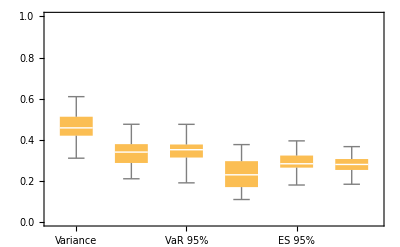

```mathematica
BoxWhiskerChart[Transpose[heInsample⟦1;;All,2;;All⟧],ChartLabels->methods,PlotRange->{0,1}]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample_box.png", %];
```

```mathematica
dates=Table[DateList[{heInsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heInsample⟦1;;All,1⟧]}];
```

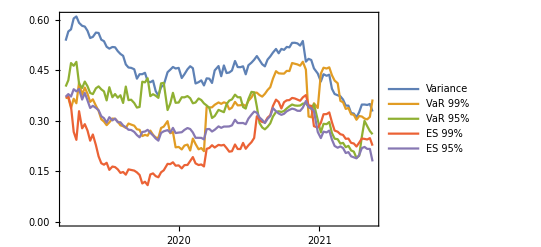

```mathematica
DateListPlot[Table[{dates,heInsample[[;;,k]]}ᵀ, {k,2,Dimensions[heInsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.png", %];
```

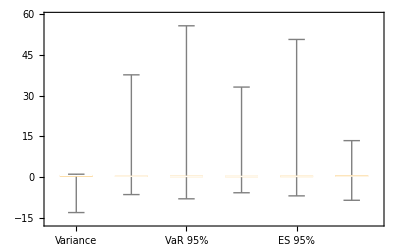

```mathematica
BoxWhiskerChart[heOutsample[[;;,2;;]]ᵀ, ChartLabels->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample_box.png", %];
```

```mathematica
dates=Table[DateList[{heOutsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heOutsample⟦1;;All,1⟧]}];
```

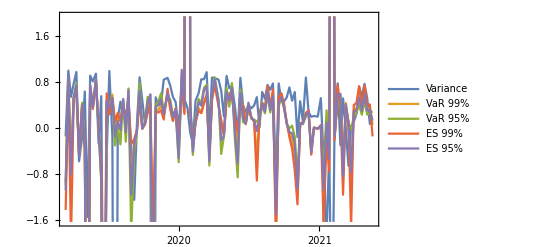

```mathematica
DateListPlot[Table[{dates,heOutsample[[;;,k]]}ᵀ, {k,2,Dimensions[heOutsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.png", %];
```

## P&L

```mathematica
data[[1,7]]
```

log return xrp

```mathematica
data[[1,6]]
```

log return future

```mathematica
data[[2,2]]
```

2019-03-11 20:00:00+00:00

### In-sample P&L

```mathematica
For[kk=0, kk≤1 111, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc = Exp[btc]-1;
rbtc = Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PL,PLbtc];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv",PLrᵀ]
]
```

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | xrp Price | log return future | log return xrp
560 | 2019-03-11 20:00:00+00:00 | 3835. | BTCJ19 Curncy | 0.312233 | -0.0142397 | -0.0182657
561 | 2019-03-08 21:00:00+00:00 | 3890. | BTCJ19 Curncy | 0.317988 | 0.00644748 | 0.010706
562 | 2019-03-07 21:00:00+00:00 | 3865. | BTCJ19 Curncy | 0.314602 | 0.00648932 | -0.0178397
563 | 2019-03-06 21:00:00+00:00 | 3840. | BTCJ19 Curncy | 0.320265 | 0.00260756 | 0.00622992
564 | 2019-03-05 21:00:00+00:00 | 3830. | BTCJ19 Curncy | 0.318276 | 0.0358842 | 0.0322186
565 | 2019-03-04 21:00:00+00:00 | 3695. | BTCJ19 Curncy | 0.308185 | -0.0332699 | -0.0331678
566 | 2019-03-01 21:00:00+00:00 | 3820. | BTCJ19 Curncy | 0.318578 | 0.0078844 | 0.0065502
567 | 2019-02-28 21:00:00+00:00 | 3790. | BTCH19 Curncy | 0.316498 | 0.0213341 | 0.0256995
568 | 2019-02-27 21:00:00+00:00 | 3710. | BTCH19 Curncy | 0.308468 | -0.0173685 | -0.0233067)

```mathematica
hvec
```

{{2019-03-11},{1.27541},{1.17717},{1.11267},{1.67389},{1.27528},{1.17723},{{0.11708529698838988, {h$108985881 -> 1.1771729795332146}},{0.0707801294840856, {h$108985881 -> 1.1126735172743183}},{0.2038613551527635, {h$108985881 -> 1.6738917193114795}},{0.1128181707068684, {h$108985881 -> 1.2752783313117233}},{0.0897521219160102, {h$108985881 -> 1.1772345759869591}}}}

### Out-of-sample P&L

```mathematica
For[kk=0, kk≤111, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv",PLrᵀ]
]
```

### Sandbox P&L in-sample

```mathematica
For[kk=0, kk≤111, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv",PLrᵀ]
]
```

### Sandbox P&L out-of-sample

```mathematica
For[kk=0, kk<=111, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv",PLrᵀ]
]
```

## Plots

In-sample
This doesn’t make much sense as the samples are overlapping, so it’s not clear which h to associate with which time period in-sample.

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

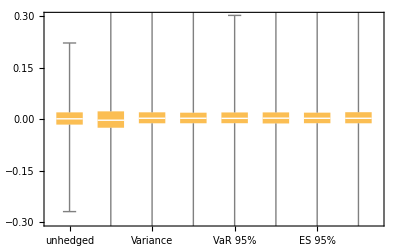

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

The overlap is clearly visible below.

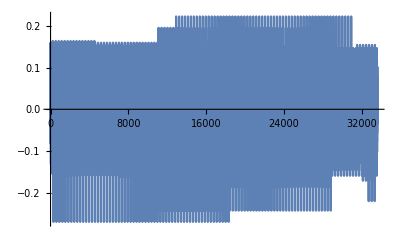

```mathematica
ListPlot[d[[2;;,2]], Joined->True,PlotRange->Full]
```

Out-of-sample

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

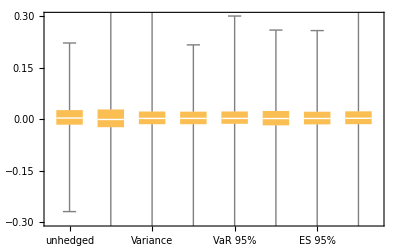

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

```mathematica
dates=Table[DateList[{d⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[d⟦2;;All,1⟧]}];
```

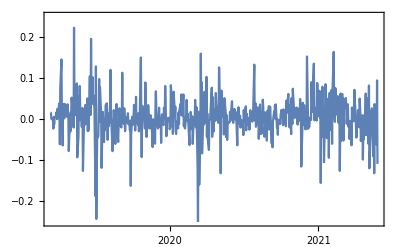
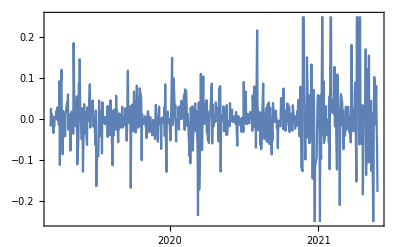

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25}], {m,2,3}]
```

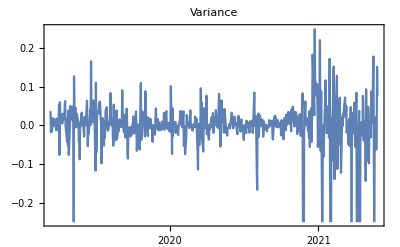
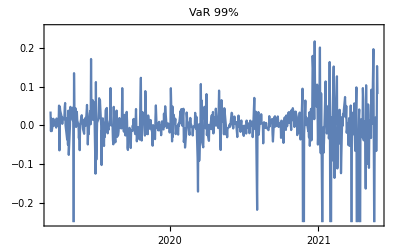
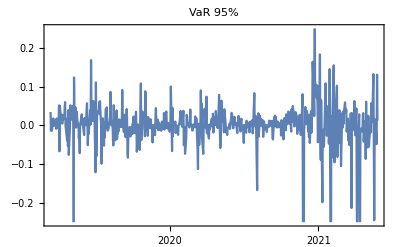
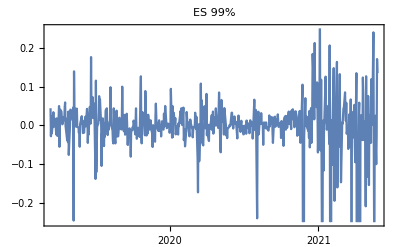
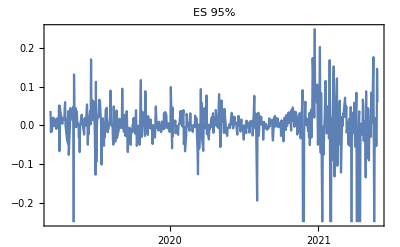
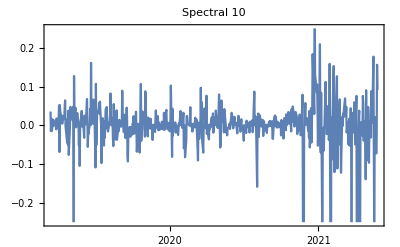

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25},PlotLabel->methods[[m-3]]], {m,4,9}]
```

Sandbox in-sample

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

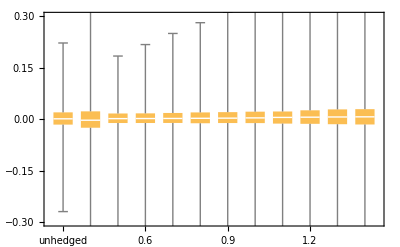

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

Sandbox out-of-sample

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

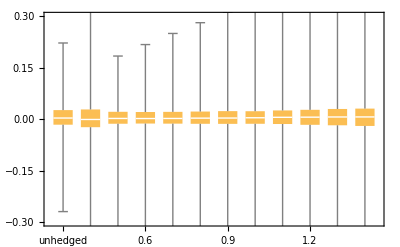

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

h time series

```mathematica
h={Join[{"Date"},methods]};
For[kk=0, kk≤111, kk++,
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
h=Join[h,{hvec[[;;-2,1]]}];
]
```

```mathematica
dates=Table[DateList[{h⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[h⟦2;;All,1⟧]}];
```

```mathematica
h
```

(Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
2021-05-20 | 1.11538 | 1.15434 | 0.711441 | 1.52542 | 1.01295 | 1.22442
2021-05-13 | 1.07182 | 1.15942 | 0.869602 | 1.36562 | 1.06467 | 1.07041
2021-05-06 | 1.07351 | 1.11736 | 0.798848 | 1.37487 | 1.04861 | 1.08509
2021-04-29 | 1.07155 | 1.13384 | 0.830714 | 1.36633 | 1.02991 | 1.06308
2021-04-22 | 1.06715 | 1.15877 | 0.794441 | 1.36331 | 1.024 | 1.04685
2021-04-15 | 1.03309 | 1.16368 | 0.735488 | 1.34625 | 0.970339 | 1.0318
2021-04-08 | 0.969477 | 1.03407 | 0.813263 | 1.34345 | 0.95076 | 0.9755
2021-04-01 | 0.934761 | 1.04314 | 0.627146 | 1.33562 | 0.934596 | 0.8726
2021-03-25 | 0.939172 | 1.04644 | 0.630865 | 1.33269 | 0.936543 | 0.865106
2021-03-18 | 0.965957 | 1.04305 | 0.658497 | 1.34599 | 0.969405 | 0.908654
2021-03-11 | 0.965838 | 1.03026 | 0.646337 | 1.3449 | 0.964745 | 0.96486
2021-03-04 | 0.99242 | 1.02629 | 0.65542 | 1.35434 | 0.983949 | 0.929664
2021-02-25 | 1.01337 | 1.02914 | 0.768105 | 1.35583 | 1.00432 | 1.01169
2021-02-18 | 1.02025 | 0.844071 | 0.746789 | 1.37689 | 0.976236 | 0.995106
2021-02-10 | 1.01951 | 1.00835 | 0.773402 | 1.38037 | 0.956037 | 1.00983
2021-02-03 | 1.05671 | 1.03647 | 0.773066 | 1.40654 | 1.01257 | 0.939061
2021-01-27 | 1.0559 | 0.972461 | 0.784011 | 1.42141 | 1.02227 | 0.923252
2021-01-20 | 1.06288 | 1.01639 | 0.784351 | 1.42027 | 1.02303 | 0.945555
2021-01-12 | 1.08295 | 0.980756 | 0.807067 | 1.41723 | 1.03261 | 0.9341
2021-01-05 | 1.03973 | 0.974752 | 0.767269 | 1.40211 | 0.983662 | 0.995577
2020-12-28 | 1.03139 | 0.930551 | 0.83832 | 1.24699 | 0.937654 | 0.9746
2020-12-18 | 0.937111 | 0.597186 | 0.863544 | 0.584419 | 0.726451 | 1.04012
2020-12-11 | 0.955209 | 0.928095 | 0.792803 | 0.972412 | 0.877392 | 0.967645
2020-12-04 | 0.95875 | 0.915587 | 0.80093 | 0.979062 | 0.88445 | 0.980294
2020-11-27 | 0.944074 | 0.969194 | 0.781118 | 1.03857 | 0.93457 | 0.896763
2020-11-19 | 0.810794 | 0.922596 | 0.790994 | 1.01878 | 0.886882 | 0.780423
2020-11-12 | 0.793544 | 0.903331 | 0.75562 | 1.00252 | 0.86803 | 0.773274
2020-11-05 | 0.789785 | 0.916373 | 0.749245 | 1.00064 | 0.845428 | 0.779921
2020-10-29 | 0.79376 | 0.911782 | 0.750055 | 0.998952 | 0.853728 | 0.775112
2020-10-22 | 0.794881 | 0.910844 | 0.76631 | 1.00252 | 0.857539 | 0.775945
2020-10-15 | 0.788306 | 0.888708 | 0.764399 | 0.995578 | 0.862372 | 0.796134
2020-10-08 | 0.781639 | 0.886524 | 0.760109 | 0.978783 | 0.842161 | 0.762079
2020-10-01 | 0.769866 | 0.882315 | 0.771213 | 0.976293 | 0.83344 | 0.743409
2020-09-24 | 0.767612 | 0.882716 | 0.773017 | 0.890088 | 0.790827 | 0.764756
2020-09-17 | 0.745238 | 0.890683 | 0.689293 | 0.971167 | 0.814949 | 0.684399
2020-09-10 | 0.756877 | 0.887649 | 0.759904 | 0.970847 | 0.828152 | 0.725318
2020-09-02 | 0.69845 | 0.868116 | 0.701162 | 0.964967 | 0.798877 | 0.66128
2020-08-26 | 0.663833 | 0.838915 | 0.634482 | 0.870082 | 0.739279 | 0.589029
2020-08-19 | 0.655597 | 0.82873 | 0.644796 | 0.87796 | 0.730905 | 0.592237
2020-08-12 | 0.635713 | 0.818256 | 0.63874 | 0.858723 | 0.717633 | 0.616251
2020-08-05 | 0.641775 | 0.831246 | 0.665657 | 0.876612 | 0.730849 | 0.624466
2020-07-29 | 0.633684 | 0.81139 | 0.636522 | 0.883382 | 0.730651 | 0.607153
2020-07-22 | 0.646119 | 0.824909 | 0.663793 | 0.885077 | 0.757185 | 0.613348
2020-07-15 | 0.638837 | 0.541417 | 0.688497 | 0.495113 | 0.630679 | 0.679617
2020-07-08 | 0.633046 | 0.480623 | 0.689274 | 0.471845 | 0.609274 | 0.660754
2020-06-30 | 0.624267 | 0.520481 | 0.705904 | 0.477446 | 0.6179 | 0.645671
2020-06-23 | 0.606535 | 0.509554 | 0.664525 | 0.483879 | 0.600801 | 0.615747
2020-06-16 | 0.624806 | 0.523018 | 0.670508 | 0.512809 | 0.638361 | 0.619252
2020-06-09 | 0.627292 | 0.511494 | 0.673388 | 0.456078 | 0.607612 | 0.66309
2020-06-02 | 0.628097 | 0.512 | 0.673388 | 0.455998 | 0.608054 | 0.663407
2020-05-26 | 0.64051 | 0.537886 | 0.677688 | 0.475241 | 0.615325 | 0.679845
2020-05-18 | 0.622017 | 0.513296 | 0.669872 | 0.452772 | 0.598727 | 0.644675
2020-05-11 | 0.619438 | 0.475687 | 0.659001 | 0.452358 | 0.598399 | 0.64264
2020-05-04 | 0.621548 | 0.515561 | 0.688708 | 0.468756 | 0.600889 | 0.636513
2020-04-27 | 0.637587 | 0.520196 | 0.677142 | 0.589982 | 0.649228 | 0.661829
2020-04-20 | 0.616326 | 0.514422 | 0.663537 | 0.494501 | 0.595761 | 0.636751
2020-04-13 | 0.637604 | 0.554243 | 0.684652 | 0.523334 | 0.645844 | 0.663286
2020-04-03 | 0.634894 | 0.58414 | 0.68739 | 0.577885 | 0.645571 | 0.649016
2020-03-27 | 0.611492 | 0.516161 | 0.667128 | 0.504086 | 0.597425 | 0.610158
2020-03-20 | 0.617178 | 0.523863 | 0.670154 | 0.481235 | 0.602593 | 0.641455
2020-03-13 | 0.623661 | 0.518781 | 0.67466 | 0.507515 | 0.64405 | 0.610034
2020-03-06 | 0.619075 | 0.380493 | 0.623239 | 0.37287 | 0.565348 | 0.719561
2020-02-28 | 0.640133 | 0.387163 | 0.628496 | 0.380039 | 0.569797 | 0.719882
2020-02-21 | 0.638314 | 0.442529 | 0.635848 | 0.379185 | 0.5636 | 0.708064
2020-02-13 | 0.62699 | 0.428968 | 0.648071 | 0.386273 | 0.549523 | 0.71068
2020-02-06 | 0.6542 | 0.444133 | 0.644769 | 0.404631 | 0.565052 | 0.753068
2020-01-30 | 0.653317 | 0.475534 | 0.618409 | 0.393379 | 0.567504 | 0.75757
2020-01-23 | 0.640117 | 0.416108 | 0.616062 | 0.366235 | 0.560393 | 0.691953
2020-01-15 | 0.634429 | 0.402726 | 0.590158 | 0.360419 | 0.54494 | 0.677147
2020-01-08 | 0.626014 | 0.395986 | 0.605206 | 0.34393 | 0.536402 | 0.674745
2019-12-31 | 0.641959 | 0.452483 | 0.599248 | 0.394191 | 0.558292 | 0.685358
2019-12-23 | 0.64245 | 0.446406 | 0.604749 | 0.393611 | 0.55713 | 0.684018
2019-12-16 | 0.648402 | 0.376795 | 0.640084 | 0.368603 | 0.552532 | 0.675756
2019-12-09 | 0.644587 | 0.444701 | 0.608729 | 0.40111 | 0.558263 | 0.678159
2019-12-02 | 0.664432 | 0.61486 | 0.684138 | 0.486723 | 0.605708 | 0.685153
2019-11-22 | 0.722219 | 0.484796 | 0.69171 | 0.349795 | 0.567221 | 0.865479
2019-11-15 | 0.719333 | 0.434778 | 0.681109 | 0.343174 | 0.562674 | 0.86761
2019-11-08 | 0.701972 | 0.440442 | 0.630327 | 0.367656 | 0.554049 | 0.779575
2019-11-01 | 0.715838 | 0.462665 | 0.680377 | 0.367552 | 0.561086 | 0.754374
2019-10-25 | 0.748044 | 0.467081 | 0.705356 | 0.378655 | 0.599657 | 0.825828
2019-10-18 | 0.772971 | 0.52127 | 0.790249 | 0.448718 | 0.630659 | 0.81698
2019-10-11 | 0.777018 | 0.461848 | 0.789071 | 0.377835 | 0.629576 | 0.871018
2019-10-04 | 0.797601 | 0.52416 | 0.822975 | 0.450018 | 0.655955 | 0.821942
2019-09-27 | 0.788528 | 0.56251 | 0.780943 | 0.407724 | 0.645122 | 0.809154
2019-09-20 | 0.793038 | 0.603264 | 0.802074 | 0.467922 | 0.653651 | 0.82171
2019-09-13 | 0.771765 | 0.607615 | 0.755429 | 0.509903 | 0.647807 | 0.825918
2019-09-06 | 0.798059 | 0.611069 | 0.764954 | 0.496399 | 0.661565 | 0.849464
2019-08-29 | 0.806569 | 0.60842 | 0.778246 | 0.474975 | 0.660323 | 0.848074
2019-08-22 | 0.808446 | 0.537802 | 0.779223 | 0.477551 | 0.661233 | 0.855247
2019-08-15 | 0.819872 | 0.618483 | 0.8083 | 0.509388 | 0.692269 | 0.887934
2019-08-08 | 0.844534 | 0.688445 | 0.805883 | 0.585218 | 0.722823 | 0.885019
2019-08-01 | 0.858231 | 0.560952 | 0.793706 | 0.510172 | 0.714219 | 0.887695
2019-07-25 | 0.865871 | 0.67589 | 0.839006 | 0.573019 | 0.735571 | 0.925998
2019-07-18 | 0.882164 | 0.62064 | 0.839503 | 0.559705 | 0.738444 | 0.927202
2019-07-11 | 0.894536 | 0.695929 | 0.844412 | 0.594125 | 0.754672 | 0.918461
2019-07-03 | 0.89044 | 0.64548 | 0.887435 | 0.521564 | 0.736368 | 0.916183
2019-06-26 | 0.983846 | 0.869501 | 0.92217 | 0.676558 | 0.834458 | 1.10233
2019-06-19 | 1.05764 | 0.851343 | 0.95132 | 0.675321 | 0.881583 | 1.20326
2019-06-12 | 1.06989 | 0.886407 | 0.986852 | 0.687852 | 0.900759 | 1.16321
2019-06-05 | 1.08559 | 0.894425 | 0.969221 | 0.718176 | 0.916883 | 1.16323
2019-05-29 | 1.09108 | 0.907121 | 0.993802 | 0.822863 | 0.959508 | 1.17865
2019-05-21 | 1.06916 | 0.929807 | 0.974896 | 0.876311 | 0.958184 | 1.16682
2019-05-14 | 1.06945 | 0.974567 | 0.975867 | 0.825158 | 0.955432 | 1.16174
2019-05-07 | 1.1168 | 1.02583 | 1.14804 | 0.973356 | 1.06316 | 1.10843
2019-04-30 | 1.12121 | 1.03705 | 1.16561 | 1.02564 | 1.08014 | 1.0858
2019-04-23 | 1.0933 | 1.06217 | 1.12053 | 0.962069 | 1.02113 | 1.06248
2019-04-15 | 1.12067 | 0.991639 | 1.05374 | 1.03061 | 1.05432 | 1.16903
2019-04-08 | 1.12457 | 1.00102 | 1.09026 | 0.811988 | 0.983427 | 1.06441
2019-04-01 | 1.14454 | 1.03227 | 1.05568 | 0.941458 | 1.05162 | 1.07267
2019-03-25 | 1.24627 | 0.910104 | 1.06656 | 1.79669 | 1.08563 | 1.12908
2019-03-18 | 1.23218 | 1.20262 | 1.22391 | 1.72835 | 1.29294 | 1.12149
2019-03-11 | 1.27541 | 1.17717 | 1.11267 | 1.67389 | 1.27528 | 1.17723)

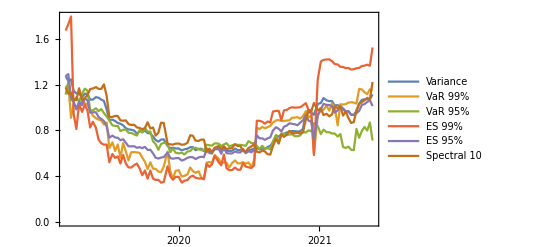

```mathematica
DateListPlot[Table[{dates,h[[2;;,k+1]]}ᵀ, {k,1,Dimensions[h][[2]]-1}],PlotLegends->methods,PlotRange->Full]
```